```mathematica
(*For the liquid phase .... (the molten salt) .... *)
```

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19},
Plot3D[N1 k T/2Log[N1]-N1 k T Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]//Log,{P,10^4,10^8},{T,600,2000},PlotStyle->Blue]
]
```

-Graphics3D-

```mathematica
(*For the gaseous phase .... (the plasma gas :) ) .... *)
```

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34),N1=6.023*10^19},
Plot3D[ N1 k T Log[N1]-N1 k T Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))]//Log,{P,10^4,10^8},{T,600,2000},PlotStyle->"Rainbow"]
]
```

-Graphics3D-

```mathematica
(*For the solid phase .... (the actual salt) ) .... *)
```

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19},
Plot3D[N1 k T Log[N1]-k T Log10[Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]]],{P,10^4,10^8},{T,600,2000}]
]
```

-Graphics3D-

```mathematica
(* Combine the three phase plots .... *)
```

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34)},
Show[ (*Liquid phase*)
Plot3D[N1 k T/2Log[N1]-N1 k T Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]//Log,{P,10^4,10^8},{T,100,2000},PlotStyle->Blue],
Plot3D[ (*Gaseous phase*)N1 k T Log[N1]-N1 k T Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))]//Log,{P,10^4,10^8},{T,100,2000},PlotStyle->"Rainbow"],
Plot3D[(*Solid phase*)N1 k T Log[N1]-k T Log10[Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]]],{P,10^4,10^8},{T,100,2000}],
PlotRange->All
]
]
```

-Graphics3D-

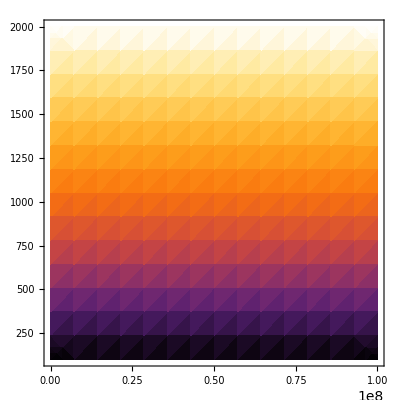

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34)},
Show[ (*Liquid phase*)
DensityPlot[N1 k T/2Log[N1]-N1 k T Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]//Log,{P,10^4,10^8},{T,100,2000},ColorFunction->"Rainbow"],
DensityPlot[ (*Gaseous phase*)N1 k T Log[N1]-N1 k T Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))]//Log,{P,10^4,10^8},{T,100,2000}
,ColorFunction->"BlueGreenYellow"],
DensityPlot[(*Solid phase*)N1 k T Log[N1]-k T Log10[Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]]],{P,10^4,10^8},{T,100,2000},ColorFunction->"SunsetColors"],
PlotRange->All
]
]
```

```mathematica
(* .... Phase transitions curves .... *)
```

```mathematica
(*Liquid-gas phase transition*)
```

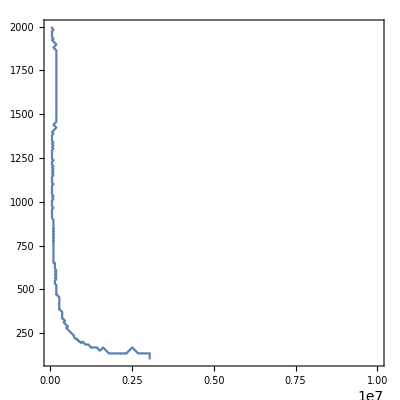

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34)},
ContourPlot[Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]==Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))],{P,10^4,10^7},{T,100,2000}]
]
```

```mathematica
(* Solid-gas phase transition *)
```

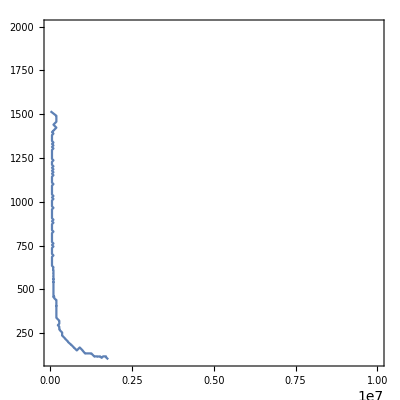

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34)},
ContourPlot[Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))]== Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]],{P,10^4,10^7},{T,100,2000}]
]
```

```mathematica
(* Solid-liquid phase transition *)
```

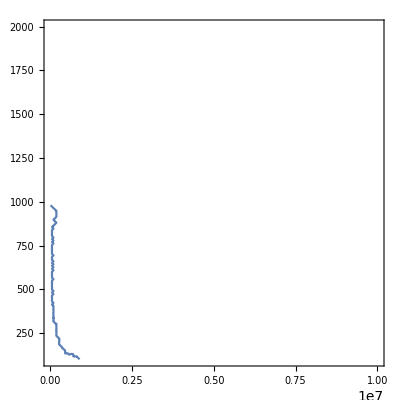

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34)},
ContourPlot[Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]== Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]],{P,10^4,10^7},{T,100,2000}]
]
```

```mathematica
(* Now combine all the 3 phases .... *)
```

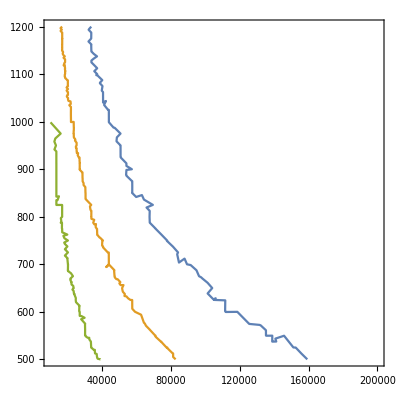

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34)},
ContourPlot[{Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]==Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))],Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))]== Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]],Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]== Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]]},{P,10^4,2*10^5},{T,500,1200}]
]
```

```mathematica
(* ... Triple point ... *)
```

```mathematica
Block[
{k=1.38*10^(-23),q=1.6*10^(-19),E0=5.78*10^8,N1=6.023*10^19,ra=174*10^(-12),rc=181*10^(-12),m=9.1*10^(-31),h=6.63*10^(-34),P,T},
FindRoot[
{
Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]]==Abs[1/(27 E0 q (P/(k T))^(8/3))2 √2 π^(3/2) ((k m T)/h)^(3/2) (108 ⅇ^(-(E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3)-108 ⅇ^((E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3)-2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (-E0 q+12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^(-(E0 q rc)/(k T)) π (E0 q+12 P rc^2) (P/(k T))^(1/6) (-(E0 q)/(k T))^(3/2) BesselJ[1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+2 ⅇ^((E0 q ra)/(k T)) π (E0 q-12 P ra^2) (P/(k T))^(1/6) ((E0 q)/(k T))^(3/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^(-(E0 q rc)/(k T)) E0 π q (1+(2 E0 q rc)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+4 √3 ⅇ^((E0 q ra)/(k T)) E0 π q (1-(2 E0 q ra)/(k T)) (P/(k T))^(2/3) BesselJ[2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-(8 √3 ⅇ^(-(E0 q rc)/(k T)) E0^2 π q^2 rc (P/(k T))^(2/3) BesselJ[4/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(8 √3 ⅇ^((E0 q ra)/(k T)) E0^2 π q^2 ra (P/(k T))^(2/3) BesselJ[4/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)-12 ⅇ^(-(E0 q rc)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-12 ⅇ^((E0 q ra)/(k T)) E0 π q (P/(k T))^(2/3) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]+24 √3 ⅇ^(-(E0 q rc)/(k T)) P π rc (P/(k T))^(1/6) √(-(E0 q)/(k T)) BesselY[-1/3,(2 (-(E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-24 √3 ⅇ^((E0 q ra)/(k T)) P π ra (P/(k T))^(1/6) √((E0 q)/(k T)) BesselY[-1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-108 ⅇ^(-(E0 q ra)/(k T)) P ra (P/(k T))^(1/3) Gamma[4/3]+108 ⅇ^((E0 q rc)/(k T)) P rc (P/(k T))^(1/3) Gamma[4/3]+27 ⅇ^(-(E0 q ra)/(k T)) P Gamma[5/3]-27 ⅇ^((E0 q rc)/(k T)) P Gamma[5/3]-108 ⅇ^((E0 q ra)/(k T)) P ra^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3)/(27 k^2 P T^2)]+108 ⅇ^(-(E0 q rc)/(k T)) P rc^2 (P/(k T))^(2/3) HypergeometricPFQ[{1},{1/3,2/3},(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^((E0 q ra)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)]+27 ⅇ^(-(E0 q rc)/(k T)) E0 q (P/(k T))^(2/3) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(27 k^2 P T^2)]+(54 ⅇ^((E0 q ra)/(k T)) E0^2 q^2 ra (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 ⅇ^(-(E0 q rc)/(k T)) E0^2 q^2 rc (P/(k T))^(2/3) HypergeometricPFQ[{2},{4/3,5/3},(E0^3 q^3)/(27 k^2 P T^2)])/(k T))],
Abs[1/(108 (P/(k T))^(5/2))((√2 E0^3 π q^3 BesselJ[1/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[1/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]+(√2 E0^3 π q^3 BesselJ[5/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k^3 √(-(E0 q)/(k T)) T^3)+8 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))]-√2 π ((E0 q)/(k T))^(5/2) BesselJ[5/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))]-(24 E0 π q √(P/(k T)) BesselY[-2/3,(-(E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-(48 E0 π q √(P/(k T)) BesselY[-2/3,(2 ((E0 q)/(k T))^(3/2))/(3 √3 √(P/(k T)))])/(k T)+(24 E0 π q √(P/(k T)) BesselY[-2/3,((E0 q)/(k T))^(3/2)/(3 √6 √(P/(k T)))])/(k T)-108 (P/(k T))^(5/6) Gamma[5/3]+(108 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(27 k^2 P T^2)])/(k T)-(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},-(E0^3 q^3)/(216 k^2 P T^2)])/(k T)+(54 E0 q √(P/(k T)) HypergeometricPFQ[{2},{2/3,4/3},(E0^3 q^3)/(216 k^2 P T^2)])/(k T))]== Abs[k T/9/P(2π (q E0 N1^(2/3)/k/T)^(3/2)Sqrt[k T/P])(BesselJ[1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)]-BesselJ[-1/3,2/3Sqrt[k T/P](q E0 N1^(2/3)/k/T)^(3/2)])+k T/P HypergeometricPFQ[{1},{1/3,2/3},-(E0^3 q^3 N1^2)/(27 k^2 P T^2)]]
}
,{{P,10},{T,1400}}]
]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{P→9.9985,T→1400.}